```mathematica
DropSequence[symbol_,n_]:=Block[{name=SymbolName[symbol],result, current=Null,node,set={},new,highlight={},max},
result=name;
max=StringLength[StringDelete[name,"x"]]-1;
For[current=max,current> n, current--,
node=ToString[current];
If[StringEndsQ[result,"x"<>node],
new=StringDrop[result,-2];
If[current>3,
highlight=Append[highlight,result->new]
];
,
new=StringDelete[result,node]
];
set=Append[set,result->new];
result=new;
];
{set,highlight}
]
```

```mathematica
Table[DropSequence[s,3],{s,{nx1x234x56,nx1x234x5x6,nx1x23x4x5x6,nx15x234x6,nx16x234x5,nx16x2345}}]
```

{{{nx1x234x56→nx1x234x5,nx1x234x5→nx1x234,nx1x234→nx1x23},{nx1x234x5→nx1x234}},{{nx1x234x5x6→nx1x234x5,nx1x234x5→nx1x234,nx1x234→nx1x23},{nx1x234x5x6→nx1x234x5,nx1x234x5→nx1x234}},{{nx1x23x4x5x6→nx1x23x4x5,nx1x23x4x5→nx1x23x4,nx1x23x4→nx1x23},{nx1x23x4x5x6→nx1x23x4x5,nx1x23x4x5→nx1x23x4,nx1x23x4→nx1x23}},{{nx15x234x6→nx15x234,nx15x234→nx1x234,nx1x234→nx1x23},{nx15x234x6→nx15x234}},{{nx16x234x5→nx1x234x5,nx1x234x5→nx1x234,nx1x234→nx1x23},{nx1x234x5→nx1x234}},{{nx16x2345→nx1x2345,nx1x2345→nx1x234,nx1x234→nx1x23},{}}}

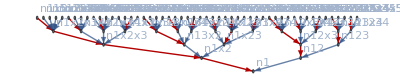

```mathematica
Block[
{result={},subedges,subhighlight,highlight={}},
Table[
With[
{
form=allGraphs5[k,"colofourrealnull"]
},
{subedges,subhighlight}=DropSequence[form,1];
result=Join[result,subedges];
highlight=Join[highlight,subhighlight];
]
,{k,allGraphs5NullAtomKeys}
]
;
result=DeleteDuplicates[result];
Graph[result,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", ImageSize->Large,GraphHighlight->highlight]
]
```

```mathematica
labels=Association[];
```

```mathematica
With[{form=allGraphs5[k5Key,"colofourrealnull"]},
Table[
With[
{f=allGraphs5[v,"colofourrealnull"]},

labels[f]=Coefficient[form,f]
],
{v,allGraphs5NullAtomKeys}
]
]
```

{1,-1,2,-6,24,-6,-2,2,-6,-2,2,-2,1,-2,1,1,-1,2,-6,-2,2,-2,1,-2,1,1,-1,2,-2,1,-2,1,1,-1,1,-2,1,1,-1,2,-6,2,1,-1,2,1,-1,1,-1,2,-1,-1}

```mathematica
With[{form=allGraphs6[K6Key,"colofourrealnull"]},
Table[
With[
{f=allGraphs6[v,"colofourrealnull"]},

labels[f]=Coefficient[form,f]
],
{v,allGraphs6NullAtomKeys}
]
]
```

{1,-1,2,-6,24,-120,24,6,-6,24,6,-6,6,-2,4,-2,-2,2,-6,24,6,-6,6,-2,4,-2,-2,2,-6,6,-2,4,-2,-2,2,-2,4,-2,-2,1,-2,6,-2,-1,1,-2,-1,1,-1,1,-2,1,1,-1,2,-6,24,6,-6,6,-2,4,-2,-2,2,-6,6,-2,4,-2,-2,2,-2,4,-2,-2,1,-2,6,-2,-1,1,-2,-1,1,-1,1,-2,1,1,-1,2,-6,6,-2,4,-2,-2,2,-2,4,-2,-2,1,-2,6,-2,-1,1,-2,-1,1,-1,1,-2,1,1,-1,2,-2,4,-2,-2,1,-2,6,-2,-1,1,-2,-1,1,-1,1,-2,1,1,-1,1,-2,6,-2,-1,1,-2,-1,1,-1,1,-2,1,1,-1,2,-6,24,-6,-2,2,-6,-2,2,-2,1,-2,1,1,-1,2,-6,-2,2,-2,1,-2,1,1,-1,2,-2,1,-2,1,1,-1,1,-2,1,1,-1,2,-6,2,1,-1,2,1,-1,1,-1,2,-1,-1}

```mathematica
With[{form=allGraphs[K4Key,"colofourrealnull"]},
Table[
With[
{f=allGraphs[v,"colofourrealnull"]},

labels[f]=Coefficient[form,f]
],
{v,realyNullAtomKeys}
]
]
```

{1,-1,-1,-1,2,-1,1,-1,1,2,-1,1,2,2,-6}

```mathematica
labels
```

<|n1x2x3x4x5→1,n12x3x4x5→-1,n123x4x5→2,n1234x5→-6,n12345→24,n1235x4→-6,n123x45→-2,n124x3x5→2,n1245x3→-6,n124x35→-2,n125x3x4→2,n125x34→-2,n12x34x5→1,n12x345→-2,n12x35x4→1,n12x3x45→1,n13x2x4x5→-1,n134x2x5→2,n1345x2→-6,n134x25→-2,n135x2x4→2,n135x24→-2,n13x24x5→1,n13x245→-2,n13x25x4→1,n13x2x45→1,n14x2x3x5→-1,n145x2x3→2,n145x23→-2,n14x23x5→1,n14x235→-2,n14x25x3→1,n14x2x35→1,n15x2x3x4→-1,n15x23x4→1,n15x234→-2,n15x24x3→1,n15x2x34→1,n1x23x4x5→-1,n1x234x5→2,n1x2345→-6,n1x235x4→2,n1x23x45→1,n1x24x3x5→-1,n1x245x3→2,n1x24x35→1,n1x25x3x4→-1,n1x25x34→1,n1x2x34x5→-1,n1x2x345→2,n1x2x35x4→-1,n1x2x3x45→-1,n1x2x3x4x5x6→1,n12x3x4x5x6→-1,n123x4x5x6→2,n1234x5x6→-6,n12345x6→24,n123456→-120,n12346x5→24,n1234x56→6,n1235x4x6→-6,n12356x4→24,n1235x46→6,n1236x4x5→-6,n1236x45→6,n123x45x6→-2,n123x456→4,n123x46x5→-2,n123x4x56→-2,n124x3x5x6→2,n1245x3x6→-6,n12456x3→24,n1245x36→6,n1246x3x5→-6,n1246x35→6,n124x35x6→-2,n124x356→4,n124x36x5→-2,n124x3x56→-2,n125x3x4x6→2,n1256x3x4→-6,n1256x34→6,n125x34x6→-2,n125x346→4,n125x36x4→-2,n125x3x46→-2,n126x3x4x5→2,n126x34x5→-2,n126x345→4,n126x35x4→-2,n126x3x45→-2,n12x34x5x6→1,n12x345x6→-2,n12x3456→6,n12x346x5→-2,n12x34x56→-1,n12x35x4x6→1,n12x356x4→-2,n12x35x46→-1,n12x36x4x5→1,n12x36x45→-1,n12x3x45x6→1,n12x3x456→-2,n12x3x46x5→1,n12x3x4x56→1,n13x2x4x5x6→-1,n134x2x5x6→2,n1345x2x6→-6,n13456x2→24,n1345x26→6,n1346x2x5→-6,n1346x25→6,n134x25x6→-2,n134x256→4,n134x26x5→-2,n134x2x56→-2,n135x2x4x6→2,n1356x2x4→-6,n1356x24→6,n135x24x6→-2,n135x246→4,n135x26x4→-2,n135x2x46→-2,n136x2x4x5→2,n136x24x5→-2,n136x245→4,n136x25x4→-2,n136x2x45→-2,n13x24x5x6→1,n13x245x6→-2,n13x2456→6,n13x246x5→-2,n13x24x56→-1,n13x25x4x6→1,n13x256x4→-2,n13x25x46→-1,n13x26x4x5→1,n13x26x45→-1,n13x2x45x6→1,n13x2x456→-2,n13x2x46x5→1,n13x2x4x56→1,n14x2x3x5x6→-1,n145x2x3x6→2,n1456x2x3→-6,n1456x23→6,n145x23x6→-2,n145x236→4,n145x26x3→-2,n145x2x36→-2,n146x2x3x5→2,n146x23x5→-2,n146x235→4,n146x25x3→-2,n146x2x35→-2,n14x23x5x6→1,n14x235x6→-2,n14x2356→6,n14x236x5→-2,n14x23x56→-1,n14x25x3x6→1,n14x256x3→-2,n14x25x36→-1,n14x26x3x5→1,n14x26x35→-1,n14x2x35x6→1,n14x2x356→-2,n14x2x36x5→1,n14x2x3x56→1,n15x2x3x4x6→-1,n156x2x3x4→2,n156x23x4→-2,n156x234→4,n156x24x3→-2,n156x2x34→-2,n15x23x4x6→1,n15x234x6→-2,n15x2346→6,n15x236x4→-2,n15x23x46→-1,n15x24x3x6→1,n15x246x3→-2,n15x24x36→-1,n15x26x3x4→1,n15x26x34→-1,n15x2x34x6→1,n15x2x346→-2,n15x2x36x4→1,n15x2x3x46→1,n16x2x3x4x5→-1,n16x23x4x5→1,n16x234x5→-2,n16x2345→6,n16x235x4→-2,n16x23x45→-1,n16x24x3x5→1,n16x245x3→-2,n16x24x35→-1,n16x25x3x4→1,n16x25x34→-1,n16x2x34x5→1,n16x2x345→-2,n16x2x35x4→1,n16x2x3x45→1,n1x23x4x5x6→-1,n1x234x5x6→2,n1x2345x6→-6,n1x23456→24,n1x2346x5→-6,n1x234x56→-2,n1x235x4x6→2,n1x2356x4→-6,n1x235x46→-2,n1x236x4x5→2,n1x236x45→-2,n1x23x45x6→1,n1x23x456→-2,n1x23x46x5→1,n1x23x4x56→1,n1x24x3x5x6→-1,n1x245x3x6→2,n1x2456x3→-6,n1x245x36→-2,n1x246x3x5→2,n1x246x35→-2,n1x24x35x6→1,n1x24x356→-2,n1x24x36x5→1,n1x24x3x56→1,n1x25x3x4x6→-1,n1x256x3x4→2,n1x256x34→-2,n1x25x34x6→1,n1x25x346→-2,n1x25x36x4→1,n1x25x3x46→1,n1x26x3x4x5→-1,n1x26x34x5→1,n1x26x345→-2,n1x26x35x4→1,n1x26x3x45→1,n1x2x34x5x6→-1,n1x2x345x6→2,n1x2x3456→-6,n1x2x346x5→2,n1x2x34x56→1,n1x2x35x4x6→-1,n1x2x356x4→2,n1x2x35x46→1,n1x2x36x4x5→-1,n1x2x36x45→1,n1x2x3x45x6→-1,n1x2x3x456→2,n1x2x3x46x5→-1,n1x2x3x4x56→-1,n1x2x3x4→1,n1x2x34→-1,n1x24x3→-1,n1x23x4→-1,n1x234→2,n14x2x3→-1,n14x23→1,n13x2x4→-1,n13x24→1,n134x2→2,n12x3x4→-1,n12x34→1,n124x3→2,n123x4→2,n1234→-6|>

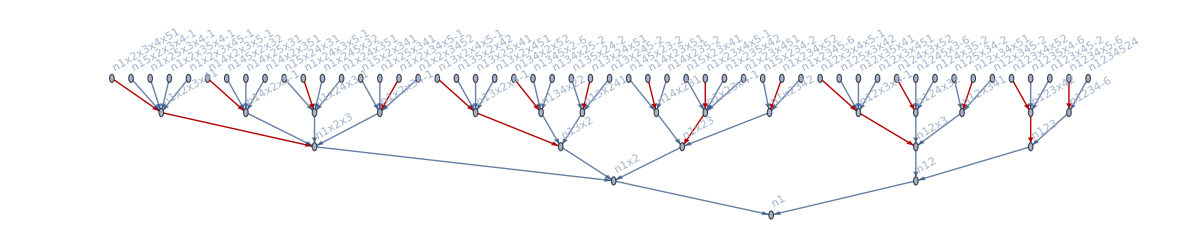

```mathematica
Block[
{result={},subedges,subhighlight,highlight={},vertices},
Table[
With[
{
form=allGraphs5[k,"colofourrealnull"]
},
{subedges,subhighlight}=DropSequence[form,1];
result=Join[result,subedges];
highlight=Join[highlight,subhighlight];
]
,{k,allGraphs5NullAtomKeys}
]
;
result=DeleteDuplicates[result];
vertices=VertexList[Graph[result]];
Graph[result,
VertexLabels->Table[v->Rotate[Row[{v,If[KeyExistsQ[labels,Symbol[v]], Style[labels[Symbol[v]],Blue],""]}],Pi/6],{v,vertices}],
GraphLayout->"LayeredDigraphEmbedding", 
ImageSize->1200,
GraphHighlight->highlight]
]
```

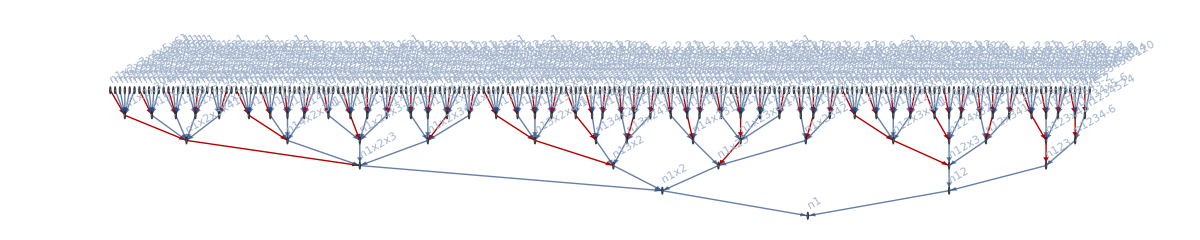

```mathematica
Block[
{result={},subedges,subhighlight,highlight={},vertices},
Table[
With[
{
form=allGraphs6[k,"colofourrealnull"]
},
{subedges,subhighlight}=DropSequence[form,1];
result=Join[result,subedges];
highlight=Join[highlight,subhighlight];
]
,{k,allGraphs6NullAtomKeys}
]
;
result=DeleteDuplicates[result];
vertices=VertexList[Graph[result]];
Graph[result,
VertexLabels->Table[v->Rotate[Row[{v,If[KeyExistsQ[labels,Symbol[v]], Style[labels[Symbol[v]],Blue],""]}],Pi/6],{v,vertices}],
GraphLayout->"LayeredDigraphEmbedding", 
ImageSize->1200,
GraphHighlight->highlight]
]
```